```mathematica
Clear["Global`*"]
$Assumptions=ω>0&&ω∈Reals&&Δ>0&&Δ∈Reals&&t>0&&t∈Reals && Ω>0&&Ω∈Reals && k∈Reals && g∈Reals && g>=0 && p∈Reals && p<=1 && p>=0 && f∈Reals && f<=1 && f>=0
```

ω>0&&ω∈ℝ&&Δ>0&&Δ∈ℝ&&t>0&&t∈ℝ&&Ω>0&&Ω∈ℝ&&k∈ℝ&&g∈ℝ&&g≥0&&p∈ℝ&&p≤1&&p≥0&&f∈ℝ&&f≤1&&f≥0

```mathematica
H=(ℏ Ω)/2({{0, 1, g}, {1, 0, 0}, {g, 0, -2k}});
```

```mathematica
Eigensystem[H]
```

{{1/2 Ω ℏ Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,1],1/2 Ω ℏ Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,2],1/2 Ω ℏ Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,3]},{{-(-2 k-Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,1])/g,-(-2 k-Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,1])/(g Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,1]),1},{-(-2 k-Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,2])/g,-(-2 k-Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,2])/(g Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,2]),1},{-(-2 k-Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,3])/g,-(-2 k-Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,3])/(g Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,3]),1}}}

```mathematica
Heig=({{0, 1, g}, {1, 0, 0}, {g, 0, -2k}})-λ IdentityMatrix[3];
MatrixForm[Heig]
computedcharpoly = -Det[Heig]
computedcharequation= (computedcharpoly==0)
```

(-λ | 1 | g
1 | -λ | 0
g | 0 | -2 k-λ)

-2 k-λ-g^2 λ+2 k λ^2+λ^3

-2 k-λ-g^2 λ+2 k λ^2+λ^3==0

```mathematica
Collect[computedcharpoly,λ]
```

-2 k+(-1-g^2) λ+2 k λ^2+λ^3

```mathematica
FullSimplify[Discriminant[computedcharpoly,λ]>=0,{g∈Reals,k∈Reals,g>=0,k>=0}]
```

True

```mathematica
a= 2k;
b=-(1+g^2);
c=-2k;
charpoly =μ^3+a μ^2+b μ+c
```

-2 k+(-1-g^2) μ+2 k μ^2+μ^3

```mathematica
FullSimplify[(charpoly/.{μ->λ})==computedcharpoly]
```

True

```mathematica
Q=FullSimplify[(3b-a^2)/9];
R=FullSimplify[(9a b -27 c -2 a^3)/54];
P = FullSimplify[R/(√(-Q^3))];
trigroots = √-Q({2 Cos[ϕ],-Cos[ϕ]-√3 Sin[ϕ],-Cos[ϕ]+√3 Sin[ϕ]}/.{ϕ->1/3 ArcCos[P]})-a/3
```

{-(2 k)/3+2/3 √(3+3 g^2+4 k^2) Cos[1/3 ArcCos[(k (18-9 g^2-8 k^2))/((3+3 g^2+4 k^2)^(3/2))]],-(2 k)/3+1/3 √(3+3 g^2+4 k^2) (-Cos[1/3 ArcCos[(k (18-9 g^2-8 k^2))/((3+3 g^2+4 k^2)^(3/2))]]-√3 Sin[1/3 ArcCos[(k (18-9 g^2-8 k^2))/((3+3 g^2+4 k^2)^(3/2))]]),-(2 k)/3+1/3 √(3+3 g^2+4 k^2) (-Cos[1/3 ArcCos[(k (18-9 g^2-8 k^2))/((3+3 g^2+4 k^2)^(3/2))]]+√3 Sin[1/3 ArcCos[(k (18-9 g^2-8 k^2))/((3+3 g^2+4 k^2)^(3/2))]])}

```mathematica
algebraicroots = FullSimplify[List @@ Roots[charpoly==0,μ][[All,2]]]
```

{1/3 (-2 k+(3+3 g^2+4 k^2)/((-9 (-2+g^2) k-8 k^3+3 √(-3 (1+g^2)^3-3 (-8+20 g^2+g^4) k^2-48 k^4))^(1/3))+(-9 (-2+g^2) k-8 k^3+3 √(-3 (1+g^2)^3-3 (-8+20 g^2+g^4) k^2-48 k^4))^(1/3)),1/6 (-4 k+((-1-ⅈ √3) (3+3 g^2+4 k^2))/((-9 (-2+g^2) k-8 k^3+3 √(-3 (1+g^2)^3-3 (-8+20 g^2+g^4) k^2-48 k^4))^(1/3))+ⅈ (ⅈ+√3) (-9 (-2+g^2) k-8 k^3+3 √(-3 (1+g^2)^3-3 (-8+20 g^2+g^4) k^2-48 k^4))^(1/3)),1/6 (-4 k+(ⅈ (ⅈ+√3) (3+3 g^2+4 k^2))/((-9 (-2+g^2) k-8 k^3+3 √(-3 (1+g^2)^3-3 (-8+20 g^2+g^4) k^2-48 k^4))^(1/3))-ⅈ (-ⅈ+√3) (-9 (-2+g^2) k-8 k^3+3 √(-3 (1+g^2)^3-3 (-8+20 g^2+g^4) k^2-48 k^4))^(1/3))}

```mathematica
symbolicroots = {Root[charpoly,μ,3],Root[charpoly,μ,1],Root[charpoly,μ,2]}
```

{Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,3],Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,1],Root[-2 k+(-1-g^2) #1+2 k #1^2+#1^3&,2]}

```mathematica
Manipulate[
{N[trigroots/.{g->gm,k->km,f->fm}],
N[Re[algebraicroots]/.{g->gm,k->km,f->fm}],
N[symbolicroots/.{g->gm,k->km,f->fm}]}
,{gm,-10,10},{km,-10,10},{fm,0,1}]
```

```mathematica
computedwf=FullSimplify[({{μ1+2 k, μ2+2 k, μ3+2 k}, {(μ1+2 k)/μ1, (μ2+2 k)/μ2, (μ3+2 k)/μ3}, {g, g, g}}).({{E^(-ⅈ μ1 t/2), 0, 0}, {0, E^(-ⅈ μ2 t/2), 0}, {0, 0, E^(-ⅈ μ3 t/2)}}).Inverse[({{μ1+2 k, μ2+2 k, μ3+2 k}, {(μ1+2 k)/μ1, (μ2+2 k)/μ2, (μ3+2 k)/μ3}, {g, g, g}})].({{√p}, {0}, {√(1-p)}})]
```

{{1/(2 g k (μ1-μ2) (μ1-μ3) (μ2-μ3))(ⅇ^(-1/2 ⅈ t (μ1+μ2+μ3)) √(1-p) (2 k+μ1) (2 k+μ2) (2 k+μ3) (ⅇ^(1/2 ⅈ t (μ1+μ3)) μ2 (μ1-μ3)-ⅇ^(1/2 ⅈ t (μ2+μ3)) μ1 (μ2-μ3)-ⅇ^(1/2 ⅈ t (μ1+μ2)) (μ1-μ2) μ3)-2 g k √p (ⅇ^(-1/2 ⅈ t μ2) μ2 (2 k+μ2) (μ1-μ3)-ⅇ^(-1/2 ⅈ t μ1) μ1 (2 k+μ1) (μ2-μ3)-ⅇ^(-1/2 ⅈ t μ3) (μ1-μ2) μ3 (2 k+μ3)))},{-1/(2 g k (μ1-μ2) (μ1-μ3) (μ2-μ3))(2 g k √p (ⅇ^(-1/2 ⅈ t μ2) (2 k+μ2) (μ1-μ3)-ⅇ^(-1/2 ⅈ t μ1) (2 k+μ1) (μ2-μ3)-ⅇ^(-1/2 ⅈ t μ3) (μ1-μ2) (2 k+μ3))+ⅇ^(-1/2 ⅈ t (μ1+μ2+μ3)) √(1-p) (2 k+μ1) (2 k+μ2) (2 k+μ3) (ⅇ^(1/2 ⅈ t (μ1+μ2)) (μ1-μ2)+ⅇ^(1/2 ⅈ t (μ2+μ3)) (μ2-μ3)+ⅇ^(1/2 ⅈ t (μ1+μ3)) (-μ1+μ3)))},{1/(2 k (μ1-μ2) (μ1-μ3) (μ2-μ3))ⅇ^(-1/2 ⅈ t (μ1+μ2+μ3)) (-ⅇ^(1/2 ⅈ t (μ1+μ2)) (μ1-μ2) (4 k^2 √(1-p)-2 g k √p+√(1-p) μ1 μ2+2 k √(1-p) (μ1+μ2)) μ3+ⅇ^(1/2 ⅈ t (μ1+μ3)) μ2 (μ1-μ3) (4 k^2 √(1-p)-2 g k √p+√(1-p) μ1 μ3+2 k √(1-p) (μ1+μ3))-ⅇ^(1/2 ⅈ t (μ2+μ3)) μ1 (μ2-μ3) (4 k^2 √(1-p)-2 g k √p+√(1-p) μ2 μ3+2 k √(1-p) (μ2+μ3)))}}

```mathematica
manualwf= 1/(2g k (μ1-μ2) (μ3-μ1) (μ2-μ3))*
{{
  + ⅇ^(-1/2 ⅈ t μ1)           μ1(2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p)
+ ⅇ^(-1/2 ⅈ t μ2)          μ2(2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p)
+ⅇ^(-1/2 ⅈ t μ3)           μ3(2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)
},{
    + ⅇ^(-1/2 ⅈ t μ1)               (2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p)
 + ⅇ^(-1/2 ⅈ t μ2)              (2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p)
 +ⅇ^(-1/2 ⅈ t μ3)               (2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)
},{
  + ⅇ^(-1/2 ⅈ t μ1)                                g μ1(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p)
+ⅇ^(-1/2 ⅈ t μ2)                               g  μ2(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p)
+ⅇ^(-1/2 ⅈ t μ3)                              g   μ3(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)
}};
```

```mathematica
FullSimplify[manualwf==computedwf]
```

True

```mathematica
Manipulate[Plot[
{Evaluate@(Abs[manualwf]^2/.{μ1->trigroots[[1]],μ2->trigroots[[2]],μ3->trigroots[[3]]}/.{k->kman,g->gman,p->pman})},{t,0,4π},PlotRange->{0,1},PlotStyle->{Blue,Green,Red}],{{kman,10},0,20},{{gman,1.0},0,10},{{pman,1},0,1}]
```

```mathematica
normalisation=1/(2g k (μ1-μ2) (μ3-μ1) (μ2-μ3))^2;
```

```mathematica
averages=normalisation*{
    (μ1(2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p))^2
+(μ2(2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p))^2 
+(μ3(2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p))^2,
     ((2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p))^2 
+((2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p))^2 
+((2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p))^2,
g^2*((μ1(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p))^2 
+(μ2(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p))^2 
+(μ3(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p))^2)
};
```

```mathematica
beatAmplitudes=2*normalisation*{
{
μ1(2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p)μ2(2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p),
μ3(2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)μ1(2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p),
μ2(2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p) μ3(2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)
},
{
(2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p)(2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p),
(2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)(2 k+μ1)(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p),
(2 k+μ2)(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p)(2 k+μ3)(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)
},
g^2*{
μ1(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p)μ2(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p),
μ3(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)μ1(μ2-μ3)((2 k+μ2) (2 k+μ3)√(1-p)-2 g k √p),
μ2(μ3-μ1)((2 k+μ3) (2 k+μ1)√(1-p)-2 g k √p) μ3(μ1-μ2)((2 k+μ1) (2 k+μ2)√(1-p)-2 g k √p)
}
};
```

```mathematica
beatFrequencies=π{μ1 -μ2,μ3 -μ1,μ2-μ3};
```

```mathematica
psi[pulsetime_,dratio_,gratio_,pratio_]:=(({
(averages[[1]]
+ beatAmplitudes[[1,1]]Cos[pulsetime*beatFrequencies[[1]]] 
+ beatAmplitudes[[1,2]]Cos[pulsetime*beatFrequencies[[2]]]
+ beatAmplitudes[[1,3]]Cos[pulsetime*beatFrequencies[[3]]])
,
(averages[[2]]
+ beatAmplitudes[[2,1]]Cos[pulsetime*beatFrequencies[[1]]] 
+ beatAmplitudes[[2,2]]Cos[pulsetime*beatFrequencies[[2]]] 
+ beatAmplitudes[[2,3]]Cos[pulsetime*beatFrequencies[[3]]])
,
(averages[[3]]
+ beatAmplitudes[[3,1]]Cos[pulsetime*beatFrequencies[[1]]] 
+ beatAmplitudes[[3,2]]Cos[pulsetime*beatFrequencies[[2]]] 
+ beatAmplitudes[[3,3]]Cos[pulsetime*beatFrequencies[[3]]])
})/.{μ1->trigroots[[1]],μ2->trigroots[[2]],μ3->trigroots[[3]]})/.{k->dratio,g->gratio,p->pratio}
```

```mathematica
manpoptime = Manipulate[
Plot[
Evaluate@(Re[psi[t,k,g,p]]),
{t,0,4},PlotStyle->{{Blue,Opacity[0.5]},{Green,Opacity[1]},{Red,Opacity[0.5]}},AspectRatio->Full,PlotRange->{-1,1}
],
{{k,2},0,15},{{g,1},0,10},{{p,1},0,1}
]
```

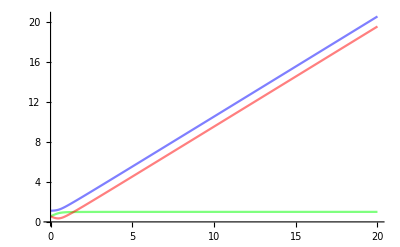

```mathematica
Plot[Evaluate@{Abs[{beatFrequencies[[1]],beatFrequencies[[2]],beatFrequencies[[3]]}/(2*π)]/.{μ1->trigroots[[1]],μ2->trigroots[[2]],μ3->trigroots[[3]]}/.{g->0.5}},{k,0,20},PlotStyle->{{Blue,Opacity[0.5]},{Green,Opacity[0.5]},{Red,Opacity[0.5]}}]
```

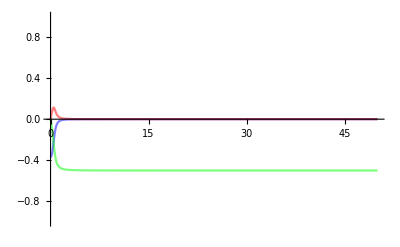

```mathematica
Plot[Evaluate[{beatAmplitudes[[2,1]],beatAmplitudes[[2,2]],beatAmplitudes[[2,3]]}/.{μ1->symbolicroots[[1]],μ2->symbolicroots[[2]],μ3->symbolicroots[[3]]}/.{g->0.6,p->1}],{k,0,50},PlotRange->{-1,1},PlotStyle->{{Blue,Opacity[0.5]},{Green,Opacity[0.5]},{Red,Opacity[0.5]}}]
```

#### Simplifcation section

Normalisation

```mathematica
simplifiedNormalisation = FullSimplify[normalisation/.{μ1->symbolicroots[[1]],μ2->symbolicroots[[2]],μ3->symbolicroots[[3]]}]
```

1/(16 g^2 k^2 ((1+g^2)^3+(-8+20 g^2+g^4) k^2+16 k^4))

```mathematica
simplifiedAverage2 = FullSimplify[FullSimplify[averages[[2]]]/.{p->1,μ1->symbolicroots[[1]],μ2->symbolicroots[[2]],μ3->symbolicroots[[3]]}]
```

((1+g^2)^2+8 (-1+2 g^2) k^2+16 k^4)/(2 ((1+g^2)^3+(-8+20 g^2+g^4) k^2+16 k^4))

```mathematica
simplifiedAverage3 = FullSimplify[FullSimplify[averages[[3]]]/.{p->1,μ1->symbolicroots[[1]],μ2->symbolicroots[[2]],μ3->symbolicroots[[3]]}]
```

(g^2 ((1+g^2)^2+12 k^2))/(2 ((1+g^2)^3+(-8+20 g^2+g^4) k^2+16 k^4))

```mathematica
AsymptoticSolve[F==2*simplifiedAverage2,{F},{k, Infinity,4}]
```

AsymptoticSolve::avars: Warning: Assumptions that involve the variables {F,k} are ignored.

{{F→1+(-48 g^2+40 g^4+8 g^6+g^8)/(256 k^4)+(-4 g^2-g^4)/(16 k^2)}}

```mathematica
AsymptoticSolve[F==2*simplifiedAverage3,{F},{k, Infinity,4}]
```

AsymptoticSolve::avars: Warning: Assumptions that involve the variables {F,k} are ignored.

{{F→(28 g^2-52 g^4+g^6)/(64 k^4)+(3 g^2)/(4 k^2)}}

```mathematica
Series[2*simplifiedAverage2,{k,0,1}]
```

1/(1+g^2)+O[k]^2

```mathematica
Series[2*simplifiedAverage3,{k,0,1}]
```

g^2/(1+g^2)+O[k]^2